```mathematica
SetOptions[ListPlot,AspectRatio->1,ImageSize->Large];
all = RandomReal[{0,1},{1000000,2}];
{insides,outsides}=GatherBy[all,√((#_⟦1⟧)^2+(#_⟦2⟧)^2)<1&];
4(Length@insides)/(Length@all)//N
```

0.858016

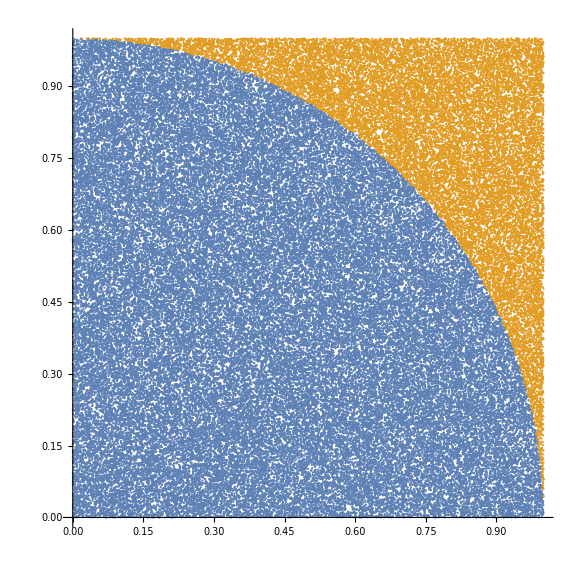

```mathematica
ListPlot@GatherBy[RandomReal[{0,1},{100000,2}],√((#_⟦1⟧)^2+(#_⟦2⟧)^2)<1&]
```